```mathematica
For an arbitrary number of moles of propane.
```

Syntax::tsntxi: "propane ." is incomplete; more input is needed.""

Syntax::sntxi: Incomplete expression; more input is needed "".

```mathematica
Solve[Γ== x^2/((a-x)(a+x)),x]
```

{{x→-(a √Γ)/(√(1+Γ))},{x→(a √Γ)/(√(1+Γ))}}

```mathematica
(* Demonstrate the solution for equilibrium computation with some initial product present *)
```

```mathematica
Manipulate[Solve[Γ== x^2/((a-x)(b+x)),x],{a,0,1},{b,0,1}]
```

```mathematica
A simpole line of code can build in the temperature-dependence of the equilibrium constant (arrhenius relation assumed):
```

```mathematica
Solve[Γ*Exp[-Ea/(k*T)]== x^2/((a-x)(b+x)),x]
```

{{x→(a Γ-b Γ-√Γ √(4 a b ⅇ^(Ea/(k T))+a^2 Γ+2 a b Γ+b^2 Γ))/(2 (ⅇ^(Ea/(k T))+Γ))},{x→(a Γ-b Γ+√Γ √(4 a b ⅇ^(Ea/(k T))+a^2 Γ+2 a b Γ+b^2 Γ))/(2 (ⅇ^(Ea/(k T))+Γ))}}

```mathematica
(* Change the stoichimetry a bit *)
```

```mathematica
Solve[Γ*Exp[-Ea/(k*T)]== x^2/((a-x)(b+x)),x]
```

{{x→(a Γ-b Γ-√Γ √(4 a b ⅇ^(Ea/(k T))+a^2 Γ+2 a b Γ+b^2 Γ))/(2 (ⅇ^(Ea/(k T))+Γ))},{x→(a Γ-b Γ+√Γ √(4 a b ⅇ^(Ea/(k T))+a^2 Γ+2 a b Γ+b^2 Γ))/(2 (ⅇ^(Ea/(k T))+Γ))}}

```mathematica
Solve[Subscript[K, a][400]== x^2/(1-x),x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.0230874},{x→0.0225664}}

```mathematica
The above derivation is missing the term to correct for the changes in the number of moles.
```

```mathematica
Solve[Subscript[K, a][400]== x^2/((1-x)(1+x)),x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.0228195},{x→0.0228195}}

```mathematica
x=0.02257;
```

```mathematica
x must be greater than zero.
```

```mathematica
Therefore the concentration of propane is1-x, in mol/L:
```

```mathematica
1-x
```

0.97743

```mathematica
The concentration of propylene and hydrogen gasin mol/L are:
```

```mathematica
x
```

0.02257

```mathematica
Clear[x]
```

```mathematica
Solve[Subscript[K, a][500]== x^2/(1-x),x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.107313},{x→0.0969129}}

```mathematica
x=0.096913
```

0.096913

```mathematica
For propane, the equilibrium concentration (mol/L)is:
```

```mathematica
1-x
```

0.903087

```mathematica
For propylene and hydrogen gas, in mol/L:
```

```mathematica
x
```

0.096913

```mathematica
Clear[x]
```

```mathematica
Solve[Subscript[K, a][600]== x^2/(1-x),x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.378656},{x→0.274656}}

```mathematica
x=0.27466
```

0.27466

```mathematica
For propane, the equilibrium concentration (mol/L)is:
```

```mathematica
1-x
```

0.72534

```mathematica
The concentration s of propylene and hydrogen gasin mol/L are:
```

```mathematica
x
```

0.27466

```mathematica
Solve[Subscript[K, a][400]== x^2/((1-x)(1-x/2)^(1/2)),x]
```

{{x→-6.728×10^51},{x→1.}}

```mathematica
Solve[Subscript[K, a][500]== x^2/((1-x)(1-x/2)),x]
```

{}

```mathematica
Solve[Subscript[K, a][600]== x^2/((1-x)(1-x/2)),x]
```

{}

```mathematica
Both processes is require high temperatures and therefore a capital cost to purchase heaters and a utility cost for continued operation.  However, the
```

```mathematica
It is possible to solve this equation for arbitrary values of the equilibrium constant, although, this solution is not necessarily practical for everyday use.
```

```mathematica
Solve[Γ==FullSimplify[ (x/(2+x/2))^2/(((1-x)/(2+x/2))((1-x/2)/(2+x/2))^(1/2))],x]
```

{{x→1/2 √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2)))-1/2 √((44 Γ^2)/(3 (4+Γ^2))-(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))-((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2))-(36 Γ^2)/((4+Γ^2) √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2)))))},{x→1/2 √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2)))+1/2 √((44 Γ^2)/(3 (4+Γ^2))-(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))-((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2))-(36 Γ^2)/((4+Γ^2) √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2)))))},{x→-1/2 √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2)))-1/2 √((44 Γ^2)/(3 (4+Γ^2))-(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))-((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2))+(36 Γ^2)/((4+Γ^2) √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2)))))},{x→-1/2 √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2)))+1/2 √((44 Γ^2)/(3 (4+Γ^2))-(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))-((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2))+(36 Γ^2)/((4+Γ^2) √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+((4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))/(3 (4+Γ^2)))))}}

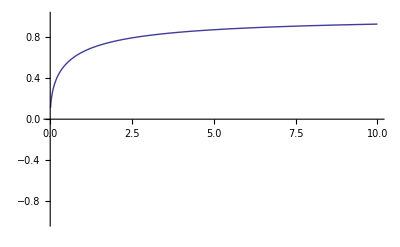

```mathematica
Plot[-1/2 √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+1/(3 (4+Γ^2))(4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+1/2 √((44 Γ^2)/(3 (4+Γ^2))-(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))-1/(3 (4+Γ^2))(4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3)+(36 Γ^2)/((4+Γ^2) √((22 Γ^2)/(3 (4+Γ^2))+(Γ^2 (-384+25 Γ^2))/(3 (4+Γ^2) (4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3))+1/(3 (4+Γ^2))(4824 Γ^4-125 Γ^6+12 √3 √(131072 Γ^6+28268 Γ^8-1125 Γ^10))^(1/3)))),{Γ,.01,10},PlotRange->1]
```

```mathematica
The above plot shows that for a reaction with these stoichiometric coefficients and initial reactant molar ratios, at equilibrium constants ca. 10 and above, the reaction nearly goes to completion.
```

```mathematica
Solve[Γ*Exp[-Ea/(k*T)]==FullSimplify[ (x/(2+x/2))^2/(((1-x)/(2+x/2))((1-x/2)/(2+x/2))^(1/2))],x]
```

{{x→1/2 √((22 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))+(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))-1/2 √((44 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))-(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))-1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3)-(36 Γ^2)/((4 ⅇ^((2 Ea)/(k T))+Γ^2) √((22 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))+(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))))},{x→1/2 √((22 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))+(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/2 √((44 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))-(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))-1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3)-(36 Γ^2)/((4 ⅇ^((2 Ea)/(k T))+Γ^2) √((22 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))+(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))))},{x→-1/2 √((22 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))+(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))-1/2 √((44 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))-(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))-1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3)+(36 Γ^2)/((4 ⅇ^((2 Ea)/(k T))+Γ^2) √((22 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))+(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))))},{x→-1/2 √((22 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))+(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/2 √((44 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))-(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))-1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3)+(36 Γ^2)/((4 ⅇ^((2 Ea)/(k T))+Γ^2) √((22 Γ^2)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))+(-384 ⅇ^((2 Ea)/(k T)) Γ^2+25 Γ^4)/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2) (4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))+1/(3 (4 ⅇ^((2 Ea)/(k T))+Γ^2))(4824 ⅇ^((2 Ea)/(k T)) Γ^4-125 Γ^6+12 √3 √(131072 ⅇ^((6 Ea)/(k T)) Γ^6+28268 ⅇ^((4 Ea)/(k T)) Γ^8-1125 ⅇ^((2 Ea)/(k T)) Γ^10))^(1/3))))}}

```mathematica
The next line solves for the equilibrium composition accepting a and b, the number of moles of reactants,as input variables.  Since these were not specified,
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/2))^2/(((a-x)/(a+b+x/2))((b-x/2)/(a+b+x/2))^(1/2))],x]
```

{{x→1/2 √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/2 √((4 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))-(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3)-(4 a (a^2+4 a b+4 b^2) Γ^2)/((4+Γ^2) √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))))},{x→1/2 √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/2 √((4 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))-(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3)-(4 a (a^2+4 a b+4 b^2) Γ^2)/((4+Γ^2) √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))))},{x→-1/2 √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/2 √((4 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))-(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3)+(4 a (a^2+4 a b+4 b^2) Γ^2)/((4+Γ^2) √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))))},{x→-1/2 √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/2 √((4 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))-(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3)+(4 a (a^2+4 a b+4 b^2) Γ^2)/((4+Γ^2) √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))))}}

```mathematica
The next line of code attempts to solve for the next most complicated case od a variable in the stoichiometry of one of the reactants;
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/c))^2/(((a-x)/(a+b+x/c))((b-x/c)/(a+b+x/c))^(1/c))],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Γ==(c x^2 ((b c-x)/((a+b) c+x))^(-1/c))/((a-x) ((a+b) c+x)),x]

```mathematica
An arbitrary solution is not available.  This may indicate that there is a lack of degree of abstraction in solving such a system.  Therefore, it makes sense to look at several cases and attempt to find a pattern.
```

```mathematica
c=1;
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/c))^2/(((a-x)/(a+b+x/c))((b-x/c)/(a+b+x/c))^(1/c))],x]
```

{{x→(a Γ+b Γ-√Γ √(4 a b+a^2 Γ-2 a b Γ+b^2 Γ))/(2 (-1+Γ))},{x→(a Γ+b Γ+√Γ √(4 a b+a^2 Γ-2 a b Γ+b^2 Γ))/(2 (-1+Γ))}}

```mathematica
c=3/4;
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/c))^2/(((a-x)/(a+b+x/c))((b-x/c)/(a+b+x/c))^(1/c))],x]
```

{{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,1]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,2]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,3]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,4]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,5]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,6]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,7]}}

```mathematica
The pound symbol (#) refers to a pure function placeholder which is undetermined in mathematica and mapping onto the solutions apce and can be substituted to any variable meeting the appropriate conditions which mathematica does not a priori programmatically know how to meet.
```

```mathematica
c=2;
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/c))^2/(((a-x)/(a+b+x/c))((b-x/c)/(a+b+x/c))^(1/c))],x]
```

{{x→1/2 √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/2 √((4 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))-(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3)-(4 a (a^2+4 a b+4 b^2) Γ^2)/((4+Γ^2) √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))))},{x→1/2 √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/2 √((4 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))-(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3)-(4 a (a^2+4 a b+4 b^2) Γ^2)/((4+Γ^2) √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))))},{x→-1/2 √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/2 √((4 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))-(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3)+(4 a (a^2+4 a b+4 b^2) Γ^2)/((4+Γ^2) √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))))},{x→-1/2 √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/2 √((4 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))-(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))-1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3)+(4 a (a^2+4 a b+4 b^2) Γ^2)/((4+Γ^2) √((2 (3 a^2+4 a b+4 b^2) Γ^2)/(3 (4+Γ^2))+(2^(1/3) ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2)))/(3 (4+Γ^2) (-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))+1/(3 2^(1/3) (4+Γ^2))(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2)+√(-4 ((3 a^2+4 a b+4 b^2)^2 Γ^4-48 a^2 b (a+b) Γ^2 (4+Γ^2))^3+(-2 (3 a^2+4 a b+4 b^2)^3 Γ^6+108 a^2 (a^2+4 a b+4 b^2)^2 Γ^4 (4+Γ^2)-288 a^2 b (a+b) (3 a^2+4 a b+4 b^2) Γ^4 (4+Γ^2))^2))^(1/3))))}}

```mathematica
c=3;
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/c))^2/(((a-x)/(a+b+x/c))((b-x/c)/(a+b+x/c))^(1/c))],x]
```

{{x→Root[27 a^5 b Γ^3+54 a^4 b^2 Γ^3+27 a^3 b^3 Γ^3+(-9 a^5 Γ^3-81 a^4 b Γ^3-153 a^3 b^2 Γ^3-81 a^2 b^3 Γ^3) #1+(21 a^4 Γ^3+78 a^3 b Γ^3+135 a^2 b^2 Γ^3+81 a b^3 Γ^3) #1^2+(-10 a^3 Γ^3-18 a^2 b Γ^3-27 a b^2 Γ^3-27 b^3 Γ^3) #1^3+(-6 a^2 Γ^3-9 a b Γ^3-9 b^2 Γ^3) #1^4+(3 a Γ^3+3 b Γ^3) #1^5+(-27+Γ^3) #1^6&,1]},{x→Root[27 a^5 b Γ^3+54 a^4 b^2 Γ^3+27 a^3 b^3 Γ^3+(-9 a^5 Γ^3-81 a^4 b Γ^3-153 a^3 b^2 Γ^3-81 a^2 b^3 Γ^3) #1+(21 a^4 Γ^3+78 a^3 b Γ^3+135 a^2 b^2 Γ^3+81 a b^3 Γ^3) #1^2+(-10 a^3 Γ^3-18 a^2 b Γ^3-27 a b^2 Γ^3-27 b^3 Γ^3) #1^3+(-6 a^2 Γ^3-9 a b Γ^3-9 b^2 Γ^3) #1^4+(3 a Γ^3+3 b Γ^3) #1^5+(-27+Γ^3) #1^6&,2]},{x→Root[27 a^5 b Γ^3+54 a^4 b^2 Γ^3+27 a^3 b^3 Γ^3+(-9 a^5 Γ^3-81 a^4 b Γ^3-153 a^3 b^2 Γ^3-81 a^2 b^3 Γ^3) #1+(21 a^4 Γ^3+78 a^3 b Γ^3+135 a^2 b^2 Γ^3+81 a b^3 Γ^3) #1^2+(-10 a^3 Γ^3-18 a^2 b Γ^3-27 a b^2 Γ^3-27 b^3 Γ^3) #1^3+(-6 a^2 Γ^3-9 a b Γ^3-9 b^2 Γ^3) #1^4+(3 a Γ^3+3 b Γ^3) #1^5+(-27+Γ^3) #1^6&,3]},{x→Root[27 a^5 b Γ^3+54 a^4 b^2 Γ^3+27 a^3 b^3 Γ^3+(-9 a^5 Γ^3-81 a^4 b Γ^3-153 a^3 b^2 Γ^3-81 a^2 b^3 Γ^3) #1+(21 a^4 Γ^3+78 a^3 b Γ^3+135 a^2 b^2 Γ^3+81 a b^3 Γ^3) #1^2+(-10 a^3 Γ^3-18 a^2 b Γ^3-27 a b^2 Γ^3-27 b^3 Γ^3) #1^3+(-6 a^2 Γ^3-9 a b Γ^3-9 b^2 Γ^3) #1^4+(3 a Γ^3+3 b Γ^3) #1^5+(-27+Γ^3) #1^6&,4]},{x→Root[27 a^5 b Γ^3+54 a^4 b^2 Γ^3+27 a^3 b^3 Γ^3+(-9 a^5 Γ^3-81 a^4 b Γ^3-153 a^3 b^2 Γ^3-81 a^2 b^3 Γ^3) #1+(21 a^4 Γ^3+78 a^3 b Γ^3+135 a^2 b^2 Γ^3+81 a b^3 Γ^3) #1^2+(-10 a^3 Γ^3-18 a^2 b Γ^3-27 a b^2 Γ^3-27 b^3 Γ^3) #1^3+(-6 a^2 Γ^3-9 a b Γ^3-9 b^2 Γ^3) #1^4+(3 a Γ^3+3 b Γ^3) #1^5+(-27+Γ^3) #1^6&,5]},{x→Root[27 a^5 b Γ^3+54 a^4 b^2 Γ^3+27 a^3 b^3 Γ^3+(-9 a^5 Γ^3-81 a^4 b Γ^3-153 a^3 b^2 Γ^3-81 a^2 b^3 Γ^3) #1+(21 a^4 Γ^3+78 a^3 b Γ^3+135 a^2 b^2 Γ^3+81 a b^3 Γ^3) #1^2+(-10 a^3 Γ^3-18 a^2 b Γ^3-27 a b^2 Γ^3-27 b^3 Γ^3) #1^3+(-6 a^2 Γ^3-9 a b Γ^3-9 b^2 Γ^3) #1^4+(3 a Γ^3+3 b Γ^3) #1^5+(-27+Γ^3) #1^6&,6]}}

```mathematica
c=4;
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/c))^2/(((a-x)/(a+b+x/c))((b-x/c)/(a+b+x/c))^(1/c))],x]
```

{{x→Root[-256 a^7 b Γ^4-768 a^6 b^2 Γ^4-768 a^5 b^3 Γ^4-256 a^4 b^4 Γ^4+(64 a^7 Γ^4+1024 a^6 b Γ^4+2880 a^5 b^2 Γ^4+2944 a^4 b^3 Γ^4+1024 a^3 b^4 Γ^4) #1+(-208 a^6 Γ^4-1488 a^5 b Γ^4-3840 a^4 b^2 Γ^4-4096 a^3 b^3 Γ^4-1536 a^2 b^4 Γ^4) #1^2+(204 a^5 Γ^4+840 a^4 b Γ^4+1920 a^3 b^2 Γ^4+2304 a^2 b^3 Γ^4+1024 a b^4 Γ^4) #1^3+(-15 a^4 Γ^4-256 a b^3 Γ^4-256 b^4 Γ^4) #1^4+(-60 a^3 Γ^4-144 a^2 b Γ^4-192 a b^2 Γ^4-128 b^3 Γ^4) #1^5+(6 a^2 Γ^4+16 a b Γ^4) #1^6+(8 a Γ^4+8 b Γ^4) #1^7+(256+Γ^4) #1^8&,1]},{x→Root[-256 a^7 b Γ^4-768 a^6 b^2 Γ^4-768 a^5 b^3 Γ^4-256 a^4 b^4 Γ^4+(64 a^7 Γ^4+1024 a^6 b Γ^4+2880 a^5 b^2 Γ^4+2944 a^4 b^3 Γ^4+1024 a^3 b^4 Γ^4) #1+(-208 a^6 Γ^4-1488 a^5 b Γ^4-3840 a^4 b^2 Γ^4-4096 a^3 b^3 Γ^4-1536 a^2 b^4 Γ^4) #1^2+(204 a^5 Γ^4+840 a^4 b Γ^4+1920 a^3 b^2 Γ^4+2304 a^2 b^3 Γ^4+1024 a b^4 Γ^4) #1^3+(-15 a^4 Γ^4-256 a b^3 Γ^4-256 b^4 Γ^4) #1^4+(-60 a^3 Γ^4-144 a^2 b Γ^4-192 a b^2 Γ^4-128 b^3 Γ^4) #1^5+(6 a^2 Γ^4+16 a b Γ^4) #1^6+(8 a Γ^4+8 b Γ^4) #1^7+(256+Γ^4) #1^8&,2]},{x→Root[-256 a^7 b Γ^4-768 a^6 b^2 Γ^4-768 a^5 b^3 Γ^4-256 a^4 b^4 Γ^4+(64 a^7 Γ^4+1024 a^6 b Γ^4+2880 a^5 b^2 Γ^4+2944 a^4 b^3 Γ^4+1024 a^3 b^4 Γ^4) #1+(-208 a^6 Γ^4-1488 a^5 b Γ^4-3840 a^4 b^2 Γ^4-4096 a^3 b^3 Γ^4-1536 a^2 b^4 Γ^4) #1^2+(204 a^5 Γ^4+840 a^4 b Γ^4+1920 a^3 b^2 Γ^4+2304 a^2 b^3 Γ^4+1024 a b^4 Γ^4) #1^3+(-15 a^4 Γ^4-256 a b^3 Γ^4-256 b^4 Γ^4) #1^4+(-60 a^3 Γ^4-144 a^2 b Γ^4-192 a b^2 Γ^4-128 b^3 Γ^4) #1^5+(6 a^2 Γ^4+16 a b Γ^4) #1^6+(8 a Γ^4+8 b Γ^4) #1^7+(256+Γ^4) #1^8&,3]},{x→Root[-256 a^7 b Γ^4-768 a^6 b^2 Γ^4-768 a^5 b^3 Γ^4-256 a^4 b^4 Γ^4+(64 a^7 Γ^4+1024 a^6 b Γ^4+2880 a^5 b^2 Γ^4+2944 a^4 b^3 Γ^4+1024 a^3 b^4 Γ^4) #1+(-208 a^6 Γ^4-1488 a^5 b Γ^4-3840 a^4 b^2 Γ^4-4096 a^3 b^3 Γ^4-1536 a^2 b^4 Γ^4) #1^2+(204 a^5 Γ^4+840 a^4 b Γ^4+1920 a^3 b^2 Γ^4+2304 a^2 b^3 Γ^4+1024 a b^4 Γ^4) #1^3+(-15 a^4 Γ^4-256 a b^3 Γ^4-256 b^4 Γ^4) #1^4+(-60 a^3 Γ^4-144 a^2 b Γ^4-192 a b^2 Γ^4-128 b^3 Γ^4) #1^5+(6 a^2 Γ^4+16 a b Γ^4) #1^6+(8 a Γ^4+8 b Γ^4) #1^7+(256+Γ^4) #1^8&,4]},{x→Root[-256 a^7 b Γ^4-768 a^6 b^2 Γ^4-768 a^5 b^3 Γ^4-256 a^4 b^4 Γ^4+(64 a^7 Γ^4+1024 a^6 b Γ^4+2880 a^5 b^2 Γ^4+2944 a^4 b^3 Γ^4+1024 a^3 b^4 Γ^4) #1+(-208 a^6 Γ^4-1488 a^5 b Γ^4-3840 a^4 b^2 Γ^4-4096 a^3 b^3 Γ^4-1536 a^2 b^4 Γ^4) #1^2+(204 a^5 Γ^4+840 a^4 b Γ^4+1920 a^3 b^2 Γ^4+2304 a^2 b^3 Γ^4+1024 a b^4 Γ^4) #1^3+(-15 a^4 Γ^4-256 a b^3 Γ^4-256 b^4 Γ^4) #1^4+(-60 a^3 Γ^4-144 a^2 b Γ^4-192 a b^2 Γ^4-128 b^3 Γ^4) #1^5+(6 a^2 Γ^4+16 a b Γ^4) #1^6+(8 a Γ^4+8 b Γ^4) #1^7+(256+Γ^4) #1^8&,5]},{x→Root[-256 a^7 b Γ^4-768 a^6 b^2 Γ^4-768 a^5 b^3 Γ^4-256 a^4 b^4 Γ^4+(64 a^7 Γ^4+1024 a^6 b Γ^4+2880 a^5 b^2 Γ^4+2944 a^4 b^3 Γ^4+1024 a^3 b^4 Γ^4) #1+(-208 a^6 Γ^4-1488 a^5 b Γ^4-3840 a^4 b^2 Γ^4-4096 a^3 b^3 Γ^4-1536 a^2 b^4 Γ^4) #1^2+(204 a^5 Γ^4+840 a^4 b Γ^4+1920 a^3 b^2 Γ^4+2304 a^2 b^3 Γ^4+1024 a b^4 Γ^4) #1^3+(-15 a^4 Γ^4-256 a b^3 Γ^4-256 b^4 Γ^4) #1^4+(-60 a^3 Γ^4-144 a^2 b Γ^4-192 a b^2 Γ^4-128 b^3 Γ^4) #1^5+(6 a^2 Γ^4+16 a b Γ^4) #1^6+(8 a Γ^4+8 b Γ^4) #1^7+(256+Γ^4) #1^8&,6]},{x→Root[-256 a^7 b Γ^4-768 a^6 b^2 Γ^4-768 a^5 b^3 Γ^4-256 a^4 b^4 Γ^4+(64 a^7 Γ^4+1024 a^6 b Γ^4+2880 a^5 b^2 Γ^4+2944 a^4 b^3 Γ^4+1024 a^3 b^4 Γ^4) #1+(-208 a^6 Γ^4-1488 a^5 b Γ^4-3840 a^4 b^2 Γ^4-4096 a^3 b^3 Γ^4-1536 a^2 b^4 Γ^4) #1^2+(204 a^5 Γ^4+840 a^4 b Γ^4+1920 a^3 b^2 Γ^4+2304 a^2 b^3 Γ^4+1024 a b^4 Γ^4) #1^3+(-15 a^4 Γ^4-256 a b^3 Γ^4-256 b^4 Γ^4) #1^4+(-60 a^3 Γ^4-144 a^2 b Γ^4-192 a b^2 Γ^4-128 b^3 Γ^4) #1^5+(6 a^2 Γ^4+16 a b Γ^4) #1^6+(8 a Γ^4+8 b Γ^4) #1^7+(256+Γ^4) #1^8&,7]},{x→Root[-256 a^7 b Γ^4-768 a^6 b^2 Γ^4-768 a^5 b^3 Γ^4-256 a^4 b^4 Γ^4+(64 a^7 Γ^4+1024 a^6 b Γ^4+2880 a^5 b^2 Γ^4+2944 a^4 b^3 Γ^4+1024 a^3 b^4 Γ^4) #1+(-208 a^6 Γ^4-1488 a^5 b Γ^4-3840 a^4 b^2 Γ^4-4096 a^3 b^3 Γ^4-1536 a^2 b^4 Γ^4) #1^2+(204 a^5 Γ^4+840 a^4 b Γ^4+1920 a^3 b^2 Γ^4+2304 a^2 b^3 Γ^4+1024 a b^4 Γ^4) #1^3+(-15 a^4 Γ^4-256 a b^3 Γ^4-256 b^4 Γ^4) #1^4+(-60 a^3 Γ^4-144 a^2 b Γ^4-192 a b^2 Γ^4-128 b^3 Γ^4) #1^5+(6 a^2 Γ^4+16 a b Γ^4) #1^6+(8 a Γ^4+8 b Γ^4) #1^7+(256+Γ^4) #1^8&,8]}}

```mathematica
c=1/2;
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/c))^2/(((a-x)/(a+b+x/c))((b-x/c)/(a+b+x/c))^(1/c))],x]
```

{{x→-(a+b-4 a Γ-4 b Γ)/(6 (1+2 Γ))-(-(a+b-4 a Γ-4 b Γ)^2+6 (1+2 Γ) (4 a b Γ+b^2 Γ))/(3 2^(2/3) (1+2 Γ) (-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3+√((-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3)^2+4 (-(a+b-4 a Γ-4 b Γ)^2+6 (1+2 Γ) (4 a b Γ+b^2 Γ))^3))^(1/3))+1/(6 2^(1/3) (1+2 Γ))(-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3+√((-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3)^2+4 (-(a+b-4 a Γ-4 b Γ)^2+6 (1+2 Γ) (4 a b Γ+b^2 Γ))^3))^(1/3)},{x→-(a+b-4 a Γ-4 b Γ)/(6 (1+2 Γ))+((1+ⅈ √3) (-(a+b-4 a Γ-4 b Γ)^2+6 (1+2 Γ) (4 a b Γ+b^2 Γ)))/(6 2^(2/3) (1+2 Γ) (-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3+√((-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3)^2+4 (-(a+b-4 a Γ-4 b Γ)^2+6 (1+2 Γ) (4 a b Γ+b^2 Γ))^3))^(1/3))-1/(12 2^(1/3) (1+2 Γ))(1-ⅈ √3) (-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3+√((-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3)^2+4 (-(a+b-4 a Γ-4 b Γ)^2+6 (1+2 Γ) (4 a b Γ+b^2 Γ))^3))^(1/3)},{x→-(a+b-4 a Γ-4 b Γ)/(6 (1+2 Γ))+((1-ⅈ √3) (-(a+b-4 a Γ-4 b Γ)^2+6 (1+2 Γ) (4 a b Γ+b^2 Γ)))/(6 2^(2/3) (1+2 Γ) (-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3+√((-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3)^2+4 (-(a+b-4 a Γ-4 b Γ)^2+6 (1+2 Γ) (4 a b Γ+b^2 Γ))^3))^(1/3))-1/(12 2^(1/3) (1+2 Γ))(1+ⅈ √3) (-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3+√((-2 a^3-6 a^2 b-6 a b^2-2 b^3+24 a^3 Γ+144 a^2 b Γ+270 a b^2 Γ+42 b^3 Γ-96 a^3 Γ^2-432 a^2 b Γ^2-36 a b^2 Γ^2-132 b^3 Γ^2+128 a^3 Γ^3-192 a^2 b Γ^3+96 a b^2 Γ^3-16 b^3 Γ^3)^2+4 (-(a+b-4 a Γ-4 b Γ)^2+6 (1+2 Γ) (4 a b Γ+b^2 Γ))^3))^(1/3)}}

```mathematica
c=1/3;
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/c))^2/(((a-x)/(a+b+x/c))((b-x/c)/(a+b+x/c))^(1/c))],x]
```

{«1»}

```mathematica
Next it is possible to vary the stoichiometry of both reactants as well as the product formation.  Possibly add a third reactant or a second product.
```

```mathematica
c=3/4;
```

```mathematica
Solve[Γ==FullSimplify[ (x/(a+b+x/c))^2/(((a-x)/(a+b+x/c))((b-x/c)/(a+b+x/c))^(1/c))],x]
```

{{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,1]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,2]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,3]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,4]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,5]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,6]},{x→Root[-81 a^3 b^4 Γ^3+(432 a^3 b^3 Γ^3+243 a^2 b^4 Γ^3) #1+(-864 a^3 b^2 Γ^3-1296 a^2 b^3 Γ^3-243 a b^4 Γ^3) #1^2+(768 a^3 b Γ^3+2592 a^2 b^2 Γ^3+1296 a b^3 Γ^3+81 b^4 Γ^3) #1^3+(-256 a^3 Γ^3-2304 a^2 b Γ^3-2592 a b^2 Γ^3-432 b^3 Γ^3) #1^4+(768 a^2 Γ^3+2304 a b Γ^3+864 b^2 Γ^3) #1^5+(81 a+81 b-768 a Γ^3-768 b Γ^3) #1^6+(108+256 Γ^3) #1^7&,7]}}

```mathematica
Manipulate[Solve[Γ==FullSimplify[ (x/(a+b+x/2))^2/(((a-x)/(a+b+x/2))((b-x/2)/(a+b+x/2))^(1/2))],x],{a,0.01,1},{b,0.01,1}]
```

```mathematica
Solving each of these equations does indeed indicate that each of these reactions goes to completion at the temperature specified.
```

```mathematica
Solve[1.16*10^26== (x/(2+x/2))^2/(((1-x)/(2+x/2))((1-x/2)/(2+x/2))^(1/2)),x]
```

{{x→-4.},{x→1.}}

```mathematica
Solve[5.34*10^23== (x/(2+x/2))^2/(((1-x)/(2+x/2))((1-x/2)/(2+x/2))^(1/2)),x]
```

{{x→-4.},{x→1.}}

```mathematica
Solve[8.31*10^21== (x/(2+x/2))^2/(((1-x)/(2+x/2))((1-x/2)/(2+x/2))^(1/2)),x]
```

{{x→-4.},{x→1.}}

```mathematica
The number of moles of product formed are, therefore, x=1.  And the reactants at equilibrium are zero.
```

```mathematica
The next line of code, looks at how the extent of reaction changes as a function of the equilibrium constant.
```

```mathematica
DSolve[{ca'[t]==k*ca[t]*cb[t],ca[0]==0.01,cb[0]==0.03,10==-ca[0]∫_0^(.5) 1/(-ca'[t])ⅆvar},{r[t],ca[t],cb[t],k},t]
```

DSolve::dvnoarg: The function k appears with no arguments.

DSolve[{ca'[t]==k ca[t] cb[t],ca[0]==0.01,cb[0]==0.03,10==(0.5 ca[0])/ca'[t]},{r[t],ca[t],cb[t],k},t]

```mathematica
Clear[x,k]
```

```mathematica
∫_0^(.5) 1/(k*(0.01-x)*(0.03-2x)^2)ⅆx
```

Integrate::idiv: Integral of 1/(-0.015 + x)^2\ (-0.01 + x) does not converge on {0, 0.5}.

∫_0^0.5 1/(k (0.03-2 x)^2 (0.01-x))ⅆx

```mathematica
1/k∫_0^(.5) 1/((0.01-x)/2*(2(0.01-x)-2*0.01+.03)^2/4)ⅆx
```

Integrate::idiv: Integral of 1/(-0.015 + x)^2\ (-0.01 + x) does not converge on {0, 0.5}.

(∫_0^0.5 8/((0.01+2 (0.01-x))^2 (0.01-x))ⅆx)/k